```mathematica
ö
```

```mathematica
Clear["Global`*"]
t*Exp[μ+σ*(Log[1/t]-μ)/σ]
```

1

```mathematica
Integrate[h*PDF[NormalDistribution[]][h],{h,(Log[1/t]-μ)/σ,Infinity}]
Integrate[PDF[NormalDistribution[]][h],{h,(Log[1/t]-μ)/σ,Infinity}]
```

(ⅇ^(-(μ-Log[1/t])^2/(2 σ^2)))/(√(2 π))

1/2 (1+Erf[(μ-Log[1/t])/(√2 σ)])

```mathematica
W[t_]:=σ*(ⅇ^(-(μ-Log[1/t])^2/(2 σ^2)))/(√(2 π))+1/2 (1+Erf[(μ-Log[1/t])/(√2 σ)])*Log[t]+1/2 (1+Erf[(μ-Log[1/t])/(√2 σ)])*μ;
W[t_]=W[1/t];
invW[t_]:=-W[1/t];
FullSimplify[-invW'[t],Assumptions->{t∈Reals,t>0}]
```

(1+Erf[(μ+Log[t])/(√2 σ)])/(2 t)

```mathematica
Clear[σ]
 μ=0;
Limit[(1+Erf[(μ+Log[1/t])/(√2 σ)])/(2 t),σ->0,Direction->"FromAbove",Assumptions->t>0]
Limit[(1+Exp[(μ+Log[1/t])/(√2 σ)])/t,σ->0,Direction->"FromAbove",Assumptions->t>0]
```

Piecewise[{{1/t, Log[t]<0}, {0, True}}]

ConditionalExpression[1/t, Log[t]>0]

```mathematica
Clear["Global`*"]
logi=√Log[2];
logi=1;
φ=1;
Simplify[Integrate[((φ √Log[(t/h)])/logi)^2*PDF[LogNormalDistribution[μ,σ]][h],{h,t,Infinity},Assumptions->{t>0,μ<0,σ>0,μ∈Reals,σ∈Reals}]]
Simplify[Integrate[(φ^2 Log[t/h])/logi^2*PDF[ExponentialDistribution[λ]][h],{h,t,Infinity},Assumptions->{t>0,λ>0,λ∈Reals}]]
```

-μ-(ⅇ^(-(μ-Log[t])^2/(2 σ^2)) σ)/(√(2 π))+1/2 Erfc[(μ-Log[t])/(√2 σ)] (μ-Log[t])+Log[t]

ExpIntegralEi[-t λ]

(ⅇ^(-(μ+Log[t])^2/(2 σ^2)) σ)/(√(2 π))-1/2 Erfc[(μ+Log[t])/(√2 σ)] (μ+Log[t])

Piecewise[{{ExpIntegralE[1,λ/t]-ExpIntegralE[1,t λ]-2 ⅇ^(-t λ) Log[t], t>1}, {Gamma[0,λ/t]-Gamma[0,t λ]-2 ⅇ^(-t λ) Log[t], 0<t<1}, {0, True}}]

```mathematica
v
```

```mathematica
1/2 (μ+ⅇ^(-(μ+Log[t])^2/(2 σ^2)) √(2/π) σ+μ Erf[(μ+Log[t])/(√2 σ)])+1/2 (1+Erf[(μ+Log[t])/(√2 σ)]) Log[t]
```

1/2 (μ+ⅇ^(-(μ+Log[t])^2/(2 σ^2)) √(2/π) σ+μ Erf[(μ+Log[t])/(√2 σ)])+1/2 (1+Erf[(μ+Log[t])/(√2 σ)]) Log[t]

```mathematica
Clear["Global`*"]
Q[t_]:=1/2 (μ+ⅇ^(-(μ+Log[t])^2/(2 σ^2)) √(2/π) σ+μ Erf[(μ+Log[t])/(√2 σ)])+1/2 (1+Erf[(μ+Log[t])/(√2 σ)]) Log[t];
invQ[t_]:=-Q[1/t];
Simplify[invQ'[t]]

Clear["Global`*"]
Q[t_]:=-μ-(ⅇ^(-(μ-Log[t])^2/(2 σ^2)) σ)/(√(2 π))+1/2 Erfc[(μ-Log[t])/(√2 σ)] (μ-Log[t])+Log[t];

H[t_]:=ExpIntegralEi[-t λ];
FullSimplify[Q'[t]]
FullSimplify[H'[t]]
```

(1+Erf[(μ+Log[1/t])/(√2 σ)])/(2 t)

```mathematica
(1+Erf[(μ-Log[t])/(√w2 σ)])/(2 t)
```

ⅇ^(-t λ)/t

```mathematica
(1+Erf[(μ+Log[1/t])/(√2 σ)])/(2 t)
```

```mathematica
PDF[NormalDistribution[]][h]
```

(ⅇ^(-h^2/2))/(√(2 π))

```mathematica
Clear["Global`*"]
Limit[(1+Erf[(μ+Log[t])/(√2 σ)])/(2 t),σ->0,Assumptions->t>1]
```

ConditionalExpression[Indeterminate, t>0&&μ+Log[t]<0]

```mathematica
Limit[Erf[x],x->Infinity]
```

1

```mathematica
Log[1.1]
```

ConditionalExpression[Indeterminate, μ+Log[t]>0]

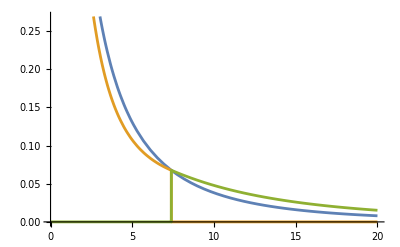

```mathematica
μ=2;σ=1;
Plot[{(1+Erf[(μ+Log[1/t])/(√2 σ)])/(2 t),(2-Exp[-((μ+Log[1/t])/(√2 σ))^2])/(2 t)*Boole[t<=Exp[μ]],Exp[-((μ+Log[1/t])/(√2 σ))^2]/(2 t)*Boole[t>Exp[μ]]},{t,0,20}]
```

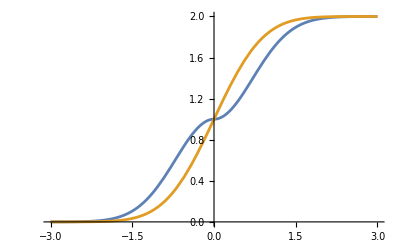

```mathematica
Plot[{(Exp[-u^2])*Boole[u<0]+(2-Exp[-u^2])*Boole[u>=0],1+Erf[u]},{u,-3,3}]
```

```mathematica
Clear["Global`*"]
σ/Sqrt[2]*Integrate[(1+Erf[u])*Exp[-(μ+Sqrt[2]*σ*u)],{u,-Infinity,Infinity}]
FullSimplify[σ/Sqrt[2]*Integrate[(Exp[-u^2])*Exp[-(μ+Sqrt[2]*σ*u)],{u,-Infinity,0}]+σ/Sqrt[2]*Integrate[(2-Exp[-u^2])*Exp[-(μ+Sqrt[2]*σ*u)],{u,0,Infinity}]]
```

ConditionalExpression[ⅇ^(-μ+σ^2/2), Re[σ]>0]

```mathematica
Exp[1/2.]
```

1.

```mathematica
Integrate[(1-1/(1+θ*Exp[-(μ+Sqrt[2]*σ*u)]))*Exp[-u^2],{u,-Infinity,0}]
```

∫_(-∞)^0 ⅇ^(-u^2) (1-1/(1+ⅇ^(-μ-√2 u σ) θ))ⅆu

```mathematica
μ=0;
Limit[(2-Exp[-((μ+Log[1/t])/(√2 σ))^2])/(2 t),σ->0,Direction->"FromAbove"]
```

ConditionalExpression[1/t, Log[1/t]∈ℝ&&1/t∈ℝ&&Log[1/t]≠0]

```mathematica
Simplify[Integrate[(1-1/(1+θ*r))*(2-Exp[-((μ+Log[1/t])/(√2 σ))^2])/(2 t),{r,0,1}]]
```

ConditionalExpression[(2 (θ-Log[1+θ])+ⅇ^(-Log[1/t]^2/(2 σ^2)) (-θ+Log[1+θ]))/(2 t θ), Re[θ]>0||-1<Re[θ]<0||θ∉ℝ]

```mathematica
Clear[μ]
Limit[(2 (θ-Log[1+θ])+ⅇ^(-Log[1/t]^2/(2 σ^2)) (-θ+Log[1+θ]))/(2 t θ),σ->0,Direction->"FromAbove"]
```

ConditionalExpression[(θ-Log[1+θ])/(t θ), ]

```mathematica
Clear["Global`*"]
u[t_]:=(μ+Log[t])/(√2 σ);
u'[t]

Solve[u[t]==u,t]
Integrate[(1+Erf[u])*ⅇ^((√2 μ-2 u σ)/(√2))*σ/Sqrt[2],{u,-Infinity,Infinity},Assumptions->σ>0]
Integrate[-(Erfc[u])*ⅇ^(-n*(√2 μ-2 u σ)/(√2))*σ/Sqrt[2],{u,Infinity,-Infinity},Assumptions->σ>0]
(*Probability that tier bigger than other tier*)
μ=-10;
σ=10;
NIntegrate[PDF[LogNormalDistribution[0,σ]][t]*CDF[LogNormalDistribution[
μ,1]][t],{t,0,Infinity}]
```

1/(√2 t σ)

{{t→ConditionalExpression[ⅇ^(-(√2 μ-2 u σ)/(√2)), -2 π≤√2 Im[√2 μ-2 u σ]<2 π]}}

ⅇ^(μ+σ^2/2)

ConditionalExpression[(ⅇ^(1/2 n (-2 μ+n σ^2)))/n, Re[n]>0]

0.840141

```mathematica
(*Arvuuttele täältä *)

WolframAlpha["(d^2/dx^2) e^(integral(f(x*t),t,0,Infinity))"]
WolframAlpha["(d^2/dx^2) Exp[f(x)]"]
WolframAlpha["(d^n/dx^n) Exp[f(x)]"]
```

WolframAlphaQueryResults

WolframAlphaQueryResults

WolframAlphaQueryResults

ⅇ+ⅇ^2/2

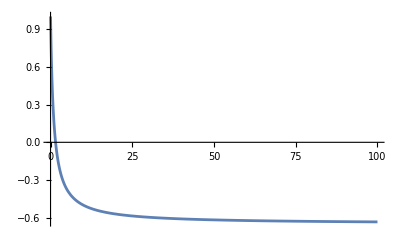

ⅇ^5+(45 ⅇ^6)/2+(315 ⅇ^7)/2+(1735 ⅇ^8)/4+(11445 ⅇ^9)/16+(34545 ⅇ^10)/32+(4865 ⅇ^11)/6+(4375 ⅇ^12)/4+(6125 ⅇ^13)/8+(238525 ⅇ^14)/432+(2877 ⅇ^15)/5+252 ⅇ^16+(16597 ⅇ^17)/48+(6951 ⅇ^18)/32+84 ⅇ^19+35 ⅇ^20+168 ⅇ^21+(105 ⅇ^22)/4+(140 ⅇ^23)/3+(126 ⅇ^25)/25+(725 ⅇ^26)/28+(180 ⅇ^27)/7+(40 ⅇ^29)/7+(45 ⅇ^33)/8+(45 ⅇ^34)/16+(10 ⅇ^41)/9+ⅇ^50/10

```mathematica
Clear["Global`*"]
κ=1;
σ=1;
μ=0;

ntht[n_]:=κ*ⅇ^(n μ+(n^2 σ^2)/2)/n;
Mn[m_]:=Sum[BellY[m,k,Table[ntht[n],{n,1,m-k+1}]],{k,0,m}];
Mn[2]
f[θ_]:=1-(θ/(θ+1))^κ*Mn[κ];
Plot[f[θ],{θ,0,100},PlotRange->Full]
Mn[10]
```

```mathematica
§
```

105/ⅇ^20

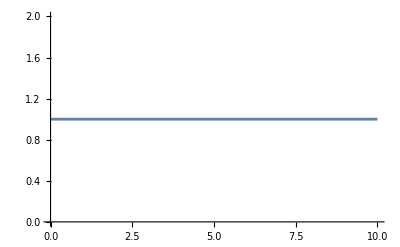

11944548597070/(189 ⅇ^100)

$Aborted

$Aborted

```mathematica
(*Without shadowing*)
Clear["Global`*"]
κ=1;
ff[t_]:=ⅇ^(-κ (EulerGamma-CoshIntegral[t]+Log[t]-SinhIntegral[t]));
Mn[m_]:=Limit[Derivative[m][ff][t],t->0];
Mn[10]
f[θ_]:=1-(θ/(θ+1))^κ*Mn[κ];
Plot[f[θ],{θ,0,10},PlotRange->Full]
```

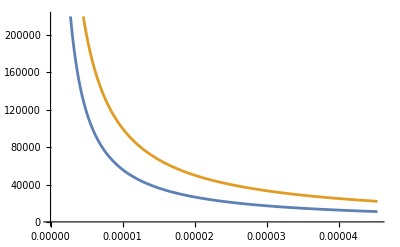

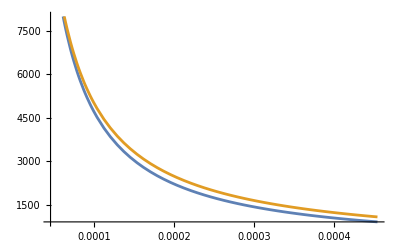

```mathematica
μ=10;σ=10;
Plot[{Erfc[(μ+Log[t])/(√2 σ)]/(2 t),1/t},{t,0,Exp[-μ]}]
Plot[{Erfc[(μ+Log[t])/(√2 σ)]/(2 t),Exp[-((μ+Log[t])/(√2 σ))^2]/(2 t)},{t,Exp[-μ],10*Exp[-μ]}]
1-Exp[-NIntegrate[Erfc[(μ+Log[t])/(√2 σ)]/(2 t),{t,Exp[-μ],Infinity}]]
Clear["Global`*"]
1-Exp[-κ*Integrate[1/t,{t,a,Exp[-μ]}]-κ*σ/Sqrt[2]*Integrate[Exp[-u^2],{u,0,Infinity}]]

1-Exp[-σ/Sqrt[2]*Integrate[Exp[-u^2],{u,a,Infinity}]]
```

```mathematica
FullSimplify[2*κ*Log[2]*(h*φ/(Sin[ϵ]^2))^(-2)*Integrate[r*(1+2^((d*r/φ)^2)*θ)^(-κ),{r,0,Infinity}]]

FullSimplify[2*κ*Log[2]*Integrate[r*(1+2^((r)^2)*θ)^(-κ),{r,0,Infinity}]]
```

ConditionalExpression[(θ^-κ Hypergeometric2F1[κ,κ,1+κ,-1/θ] Sin[ϵ]^4)/(d^2 h^2), ]

ConditionalExpression[θ^-κ Hypergeometric2F1[κ,κ,1+κ,-1/θ], (Re[1/θ]≥-1||θ∉ℝ)&&Re[κ]>0]

```mathematica
κ=1;
μ=0;
σ=0.01;
logF[t_]:=κ(1-CDF[LogNormalDistribution[μ,σ]][t])/t
expF[t_]:=κ(1-CDF[ExponentialDistribution[1/Exp[μ+σ^2/2]]][t])/t;

Plot[{logF[t],expF[t]},{t,0.1,1},PlotRange->Full]
Plot[{logF[t],expF[t]},{t,3,5},PlotRange->Full]

Mean[LogNormalDistribution[-μ,σ]]
Mean[ExponentialDistribution[1/Exp[μ+σ^2/2]]]
Moment[LogNormalDistribution[μ,σ],2]
Moment[ExponentialDistribution[1/Exp[μ+σ^2/2]],2]
```